```mathematica
Quiet@Remove["`*"]
```

## Derivations check

```mathematica
H=px^2/2+py^2/2+y*px-x*py-μ/(√((μ+x)^2+y^2))-(1-μ)/(√((1-μ-x)^2+y^2));
```

```mathematica
D[H,px]
```

px+y

```mathematica
D[H,py]
```

py-x

```mathematica
D[-H,x]
```

py+((1-μ) (1-x-μ))/((y^2+(1-x-μ)^2)^(3/2))-(μ (x+μ))/((y^2+(x+μ)^2)^(3/2))

```mathematica
D[-H,y]
```

-px-(y (1-μ))/((y^2+(1-x-μ)^2)^(3/2))-(y μ)/((y^2+(x+μ)^2)^(3/2))

## Solving Hamiltons Equations (all now functions of t)

```mathematica
Quiet@Remove["`*"]
```

```mathematica
μ=0.012151;
```

```mathematica
ics={
x[0]==0.2,
y[0]==0,
px[0]==0,
py[0]==0.2
};
```

```mathematica
H=px[t]^2/4+py[t]^2/4+y[t]*px[t]-x[t]*py[t]-μ/(√((μ+x[t])^2+y[t]^2))-(1-μ)/(√((1-μ-x[t])^2+y[t]^2))
```

px[t]^2/4+py[t]^2/4-py[t] x[t]+px[t] y[t]-0.987849/(√((0.987849-x[t])^2+y[t]^2))-0.012151/(√((0.012151+x[t])^2+y[t]^2))

```mathematica
eqn1=D[x[t],t]==D[H,px[t]]
```

x'[t]==px[t]/2+y[t]

```mathematica
eqn2=D[y[t],t]==D[H,py[t]]
```

y'[t]==py[t]/2-x[t]

```mathematica
eqn3=D[px[t],t]==D[-H,x[t]]
```

px'[t]==py[t]+(0.987849 (0.987849-x[t]))/(((0.987849-x[t])^2+y[t]^2)^(3/2))-(0.012151 (0.012151+x[t]))/(((0.012151+x[t])^2+y[t]^2)^(3/2))

```mathematica
eqn4=D[py[t],t]==D[-H,y[t]]
```

py'[t]==-px[t]-(0.987849 y[t])/(((0.987849-x[t])^2+y[t]^2)^(3/2))-(0.012151 y[t])/(((0.012151+x[t])^2+y[t]^2)^(3/2))

```mathematica
sols=NDSolve[{eqn1,eqn2,eqn3,eqn4,ics},{x[t],y[t],px[t],py[t]},t][[1]]
```

{x[t]→InterpolatingFunction[{{0., 0.}}, <>][t],y[t]→InterpolatingFunction[{{0., 0.}}, <>][t],px[t]→InterpolatingFunction[{{0., 0.}}, <>][t],py[t]→InterpolatingFunction[{{0., 0.}}, <>][t]}

### x[t] plot

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

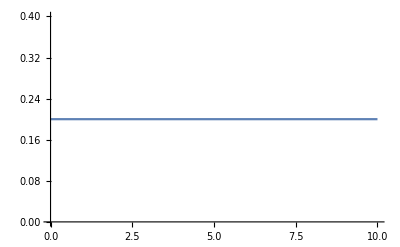

```mathematica
Plot[x[t]/.sols,{t,0,10}]
```

### y[t] plot

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

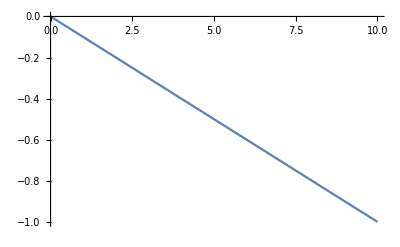

```mathematica
Plot[y[t]/.sols,{t,0,10}]
```

### (x[t],y[t]) parametric plot

InterpolatingFunction::dmval: Input value {0.000204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

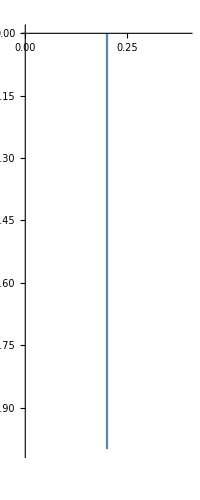

```mathematica
ParametricPlot[{x[t],y[t]}/.sols,{t,0,10}]
```

### px[t] plot

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

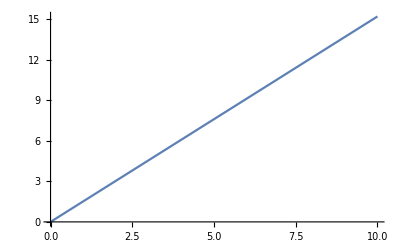

```mathematica
Plot[px[t]/.sols,{t,0,10}]
```

### py[t] plot

```mathematica
Plot[py[t]/.sols,{t,0,10}]
```

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics-